```mathematica
{R1,R2, C1,C2, L1,L2}={7.0*10^3,7.0*10^3,300.0*10^-6,700.0*10^-6,400*10^-3,200*10^-3};
TMax=123;
V[t_] :=Sin[t]
{q1Sol,q2Sol}=NDSolveValue[{
R1 (q1'[t]+q2'[t]) + q1[t]/C1+L1 (q1''[t]+q2''[t])+V[t]==0,
L2 q2''[t] + q2[t]/C2+R2 q2'[t]+q1[t]/C1==0,
q1[0]==q1'[0]==q2[0]==q2'[0]==0},{q1,q2},{t,0, TMax}]
```

{InterpolatingFunction[…],InterpolatingFunction[…]}

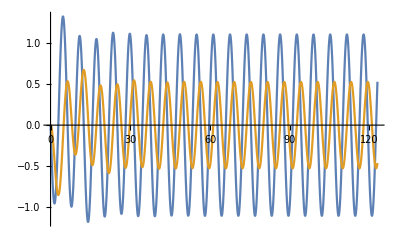

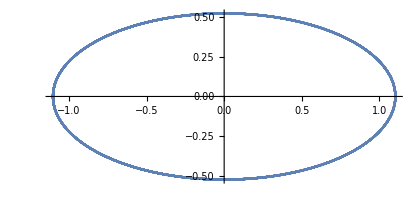

```mathematica
Plot[{R1* q1Sol'[t],q1Sol[t]/C1},{t, 0, TMax}]
ParametricPlot[{R1* q1Sol'[t],q1Sol[t]/C1},{t, TMax/2, TMax}]
```

# Experiments, Data and Models for Nonlinear Electrical Circuits

Allan Struthers and Jason Gregerson

Math Sciences, Michigan Technological University

Over 80% of the student body at MTU has a Science or Engineering major.  Essentially all of those students complete a Linear Algebra and ODE sequence.  The additional requirements for a Math minor fit reasonably well into most technical degrees and many students choose to complete a math minor.   A senior level course “Nonlinear Dynamics and Chaos” is a common elective for such students.  A project is a common component of this course.

## Abstract

We describe a sequence of simple experiments built on breadboard using standard passive (resistors, capacitors, and inductors) circuit components and a commodity analog multiplier chip. Preliminary experiments (simple RC and LRC circuits) give a natural way to extract parameter value using standard signal generator waveforms. Subsequent experiments introduce an analog multiplier chip which gives the scaled product of two input voltages. A final experiment incorporates multiplier chips into LRC based circuits to generate more interesting output.

## Background

Electrical Engineering and Physics majors in Nonlinear Dynamics and Chaos have often chosen to build a various chaotic circuits as a final project.  This is much more challenging for students than they anticipate. They struggle to build functioning circuits and explain the link between the ODE model and the circuit diagram they followed.  Last fall I decided to incorporate a circuits tutorial into this class by getting the students to construct  a circuit modelled by the chaotic Rössler [1] ODEs
	x' | = | -y-z
y' | = | x+a y
z' | = | b+z(x-c)
The primary source for this was a proposal [2] found by an earlier student group. Students reported previous experience building circuits with soldering irons and claimed to remember circuits from ODEs.

Students struggled more with building circuits than I thought they would and I started building some tutorial materials.

## Rössler Simulation

The system is simple to simulate and cleaner to plot and analyze than the better known Lorentz system.

```mathematica
{a,b,c}={0.2,0.2,5.7}; TMax=143;
{xSol,ySol,zSol}=NDSolveValue[{
x'[t]==-y[t]-z[t],
y'[t]==x[t] + a* y[t],
z'[t]==b + z[t]*(x[t]-c),x[0]==y[0]==z[0]==1.2},{x,y,z},{t, 0, TMax}];
TabView[{
"xyz"->ParametricPlot3D[{xSol[t],ySol[t],zSol[t]},{t,0, TMax},PlotRange->All,PlotPoints->10^3],
"x, y, and z"->Plot[{xSol[t],ySol[t],zSol[t]},{t,0, TMax},PlotRange->All,PlotPoints->10^3,PlotLegends->{"x","y","z"}]}]
```

12

## Chaotic Circuit

Students have been making videos of circuit builds and experiments.  Over the years most of the circuits have been kept as souvenirs or salvaged for parts.  I saved the breadboard circuit below.  It contains two LM411 op amps (the small black boxes mounted in the middle) powered by two 9V batteries and is tuned through chaotic transitions) with the two variable resistors (the visible large round objects) and consists of a bunch of resistors (the small horizontal sausage components) and capacitors which are the blockish upright components.

## Circuit Diagram from [2]

This Rössler circuit implementation is simpler than most other chaotic circuits.

-Graphics-

The inexpensive analog multiplier AD633 is the multiplicative term z(x-c) in the 3rd ODE. Fortunately the AD633 data sheet [5] is very clear. Unfortunately the loops and why it is a Rössler ODE is far from clear to most ODE students even EE and PHY majors!

## Analog Multiplier from [2]

The AD633 data sheet [5] is admirably clear.

-Graphics-

## Target

A more convincing accessible introduction to simple circuits starting from clear statements of Kirchoff’s laws and specifications of the standard passive (capacitors, resistors, and inductors) circuit elements with a goal of understanding how to construct and collect data from a circuit modelled by a Rössler like system.

## Basics and Kirchoff’s Laws

Kirchoff’s laws apply to the flow of electricity in a network of electrical components.

Electrical components (voltage sources, capacitors, resistors, inductors, etc) are connected by wires which are joined at nodes.

Capacitors store charge. Kirchoff’s laws and component properties give ODEs for the time varying charge q_i(t) stored on each capacitor in a network.

Voltage differences drive changes in the charge stored q_i(t) stored on capacitor i.  The derivative  q_i'(t) is the current through the wire with capacitor i.

## Passive Linear Electrical Components

There are only three kinds of passive electrical components. Each kind (capacitor, resistor, and inductor) is defined by an equation which gives the voltage drop across the component.

The voltage drop across a capacitor is the charge on the capacitor q divided by a constant C called capacitance.  This is frequently written Δv=q/C.  The MKS unit for capacitance is the Farad (F) and capacitances are usually in the range 10^-6 F-10^1 F.

The voltage drop across a resistor is the current i through the resistor times a constant R called resistance.  This is called Ohm’s law and is frequently written Δv=i * R. The MKS unit for resistance is the Ohm (Ω) and resistances are usually in the range 10^1 Ω-10^6 Ω.

The voltage drop across an inductor is rate of change di/dt of the current through the inductor times a constant H called inductance.  This is frequently written Δv=di/dt*H . The MKS unit for inductance is the Henry(H) and inductances are usually in the range 10^-6 H-10^0 H.

## Variable Capacitors, Resistors, and Inductors

A typical variable capacitors stores charge on overlapping metal plates.  Increasing the overlap of the plates increases the capacitance.

A typical variable resistor has an adjustable contact point (called a tap) on a resistance element.   Increasing the effective length of the resistance element increases the resistance.

The typical variable inductor has an adjustable magnetic core within a coil of wire.  Inserting the core further into the coil increases the inductance.

## Kirchoff’s Laws

Kirchoff’s  current law: The sum of currents into a node is zero.

Kirchoff’s  voltage law: The sum of voltage differences around every closed loop is zero.

## Breadboard

Breadboard has pre-connected push in slots to build circuit prototypes.  The holes fit electronic component legs. The horizontal hole strips are wired together A-E and F-J. The vertical X and Y strips are wired together.  The vertical holes are usually used for power.  The middle fits a standard form factor chip. In this case an AD633.

## Oscilloscope

An oscilloscope is a standard tool to visualize oscillating voltages.  Below is a picture of a $170 digital oscilloscope from EBay [6].  It can generate a variety of waveforms (at up to 20MHz), visualize voltages v_1(t) and v_2(t), visualize the voltages in the v_1-v_2 phase space,  and export data through USB.

## RC Circuit

The yellow probe is Ch1, the green probe is Ch2, the red and black alligator clips are the  green “GEN” square wave driving the circuit through the white wires.   Remember the breadboard has the blocks of five holes connected underneath so the RC circuit has a capacitor (brown square thing) in series with a resistor (stripey sausage thing).  The ODE is of course
	q/C+R q'-V(t)=0
where V is a square wave.   The voltages being measured are: yellow probe V(t) and green probe R q'.

## Oscilloscope: Phase Field

Here the oscilloscope is measuring the voltages in the phase field mode to the same RC circuit. You switch modes by selecting “X-Y” mode from the menu.

## RC Circuit

The RC circuit is easy to simulate and plot. Remember, we moved stuff around and scaled to make things fit because it was easy.  The oscilloscope  shows the vertical scales and offsets on the screen.

```mathematica
{R1,C1}={1.0,0.1};
TMax=5;
V=SquareWave;
qSol=NDSolveValue[{q[t]/C1+R1 q'[t]+V[t]==0,q[0]==0},q,{t,0, TMax}];
TabView[{
"v_1 & v_2"->Plot[{-R1 qSol'[t],V[t]},{t,0, TMax}],
"v_1 vs v_2"->ParametricPlot[{V[t],-R1 qSol[t]},{t,0, TMax},PlotRange->All,PlotStyle->Purple,PlotRange->All,AspectRatio->Automatic]
}]
```

12

## LRC Circuit

Every real circuit has a small physical effect (called inductance) that smooths out rapid changes in current. It is what an inductor does. It is easy to change a the driving wave form, simulate the LRC circuit and plot the results.

```mathematica
{L1,R1,C1}={0.15,1.0,0.1};
TMax=5;
V=TriangleWave;
qSol=NDSolveValue[{L1 q''[t]+q[t]/C1+R1 q'[t]+V[t]==0,q[0]==0,q'[0]==0},q,{t,0, TMax}];
TabView[{
"v_1 & v_2"->Plot[{-R1 qSol'[t],V[t]},{t,0, TMax}],
"v_1 vs v_2"->ParametricPlot[{V[t],-R1 qSol[t]},{t,0, TMax},PlotRange->All,PlotStyle->Purple,PlotRange->All,AspectRatio->Automatic]
}]
```

12

## Circuit Design

Students in the Chaos course designed circuits with at least two loops. Here is one from Sara.

You can see (in blue) that Sara used the current law to work out the connection between the currents. She used the voltage law to write down the ODEs for each loop.  She did forget to include the voltage source V included in the first loop.

## Which Loops

You can see that subtracting ODE_1 from ODE_2 eliminates the term from the central capacitor and gives the voltage law for the outer loop!  Sara expressed this as “It does not matter which loops you pick!”

A loop without an inductor gives a first order ODE.  It is not always obvious when such a loop exists! If it does you need to drop a 1st derivative initial condition.

## Sara’s Circuit (simulation)

```mathematica
{R1,R2,C1,C2,L1,L2}={7*10^3,3*10^3,300*10^-6,700*10^-6,200*10^-3,400*10^-3};
V=TriangleWave; TMax=12;
{q1Sol,q2Sol}=NDSolveValue[{
R1 q1'[t]+ q1[t]/C1+L1 q1''[t]+V[t] ==0,
L2 q2''[t]+q2[t]/C2+R2 q2'[t]+q1[t]/C1 ==0,
q1[0]==q2[0]==q1'[0]==q2'[0]==0},
{q1,q2},{t,0, TMax}(*,InterpolationOrder->5*)];
TabView[{
"V & R_1"->Plot[{V[t],R1 q1Sol'[t]},{t,0, TMax},
PlotLegends->{"V","R_1"},PlotRange->All],
"R_2 & C_1 & C_2"->Plot[{R2 q2Sol'[t],q1Sol[t]/C1,q2Sol[t]/C2},{t,0, TMax},
PlotLegends->{"R_2","C_1","C_2"},PlotRange->All],
"L_1 & L_2"->Plot[{L1 q1Sol''[t],L2 q2Sol''[t]},{t,0, TMax},
PlotLegends->{"L_1","L_2"},PlotRange->All]
}]
```

123

## Sara’s Circuit (phase plots)

The phase plots look a bit messy!

```mathematica
TabView[{
"V-R_1"->ParametricPlot[{V[t],R1 q1Sol'[t]},{t,0, TMax},
PlotRange->All,AspectRatio->1],
"R_2-C_1"->ParametricPlot[{R2 q2Sol'[t],q1Sol[t]/C1},{t,0, TMax},PlotRange->All],
"C_1-C_2"->ParametricPlot[{q1Sol[t]/C1,q2Sol[t]/C2},{t,0, TMax},PlotRange->All]
}]
```

123

## Frequency Sweep

The economy oscilloscope can not perform a standard linear frequency sweep 
	V(t)=sin(ω(t) t)
with frequency 
	ω(t)=ω_min+(ω_max-ω_min)t/T_max
to look for “resonant” frequencies between ω_min and ω_max but a simulation can. The

If transients and oscillations are fast moving slowly through frequencies will expose long time responses. An outsized response near t_* means the frequency ω(t_*) is interesting.  Here is an LRC example.

```mathematica
{L1,R1,C1}={0.1,0.01,0.1};{ωMin,ωMax}={8.0,12.0}; TMax=5000;
ω[t_]:=ωMin + (ωMax-ωMin)t/TMax
qSol=NDSolveValue[{L1 q''[t]+R1 q'[t]+q[t]/C1+Sin[ω[t]t]==0,q[0]==q'[0]==0},q,{t,0, TMax},MaxSteps->10^6];
Plot[qSol[t],{t,0, TMax},PlotRange->All,PlotPoints->10^4]
```

-Graphics-

## Frequency Response (LRC)

The non-transient response to V=sin(ω t) of the standard LRC circuit is.

```mathematica
Clear[L1,C1,R1,q,ω]
Simplify[DSolveValue[L1 q''[t]+R1 q'[t]+q[t]/C1+Sin[ω t]==0,q[t],t]/.{C[1]->0,C[2]->0} ]
```

(C1 (C1 R1 ω Cos[t ω]+(-1+C1 L1 ω^2) Sin[t ω]))/(1-2 C1 L1 ω^2+C1^2 ω^2 (R1^2+L1^2 ω^2))

The magnitude is easily computed. Here is a plot showing a strong response near ω=10.

```mathematica
NTMagnitude[{L1_,R1_,C1_}][ω_]:= (C1 √((C1 R1 ω)^2+(-1+C1 L1 ω^2)^2))/Abs[1-2 C1 L1 ω^2+C1^2 ω^2 (R1^2+L1^2 ω^2)]
TabView[{
"loglog"->LogLogPlot[NTMagnitude[{0.1,0.01,0.1}][ω],{ω,1,100},
GridLines->Automatic,Frame->True],
"log"->LogPlot[NTMagnitude[{0.1,0.01,0.1}][ω],{ω,1,100},
GridLines->Automatic,Frame->True],
"natural"->Plot[NTMagnitude[{0.1,0.01,0.1}][ω],{ω,1,100},
GridLines->Automatic,Frame->True,PlotRange->All]},3]
```

123

## Fit for LRC Sweep

The fit of a sweep is good.  This is a simulation after all.

-Graphics-

You can do the same thing for more complicated systems. Sara’s circuit has two resonances in simulation and data.

## References

[1]  Rössler, O. E.  1976
“An Equation for Continuous Chaos”, Physics Letters, 57A (5): 397–398.

[2]  Plazas,D. and Cardenas-Rodriques, J. S.  2019
“Chaotic Rössler System based on Circuits”, https://www.researchgate.net/publication/334634999_Linear_Analysis_of_Rossler_System_based_on_Circuits

[3]  Struthers, A. and Potter, M.  2019
“Differential Equations for Scientists and Engineers”, Springer

[4]  Zill D. G. (various editions and years) 
“A First Course in Differential equations with Modeling Applications”

[5]  Analog Devices
“Low Cost Analog Multiplier AD633”
https://www.analog.com/media/en/technical-documentation/data-sheets/ad633.pdf

[6] EBay Oscilloscope on 2/9/23
https://www.amazon.com/Oscilloscope-Channels-Bandwidth-Portable-SDS1102X/dp/B089GG14BP